# Data Wrangling, Model Testing, and Model Analysis for Object-Oriented Models in the Wolfram Language

## Workshop # 232 40th International System Dynamics Conference Frankfurt, Germany & Online | July 22, 2022 Guido Wolf Reichert (BSL Management Suport) and Jan Brugård (Wolfram MathCore)

## Introduction

Wolfram Language?! Why should we bring models to programming environments?

### Let’s take 5 minutes to introduce Wolfram Mathematica \[MathematicaIcon] and the Wolfram Language\[WolframLanguageLogo]

#### Functional programming & symbolic computation

Mathematica (the main platform to run the Wolfram Language) is a Computer Algebra System (CAS).
Everything is essentially an expression, where the head can be thought of as a kind of label or type:

head[ e_1, e_2, ...]

Looking at atomic expressions (we cannot split them further into subexpressions), we see that symbols are first class citizens:

```mathematica
AllTrue[ { 1, 1.2, "Hello", x }, AtomQ ]
```

True

```mathematica
Map[Head] @ { 1, 1.2, "Hello", x }
```

{Integer,Real,String,Symbol}

In the WL we can immediately do symobolic, mathematical computation.

```mathematica
x * x
```

x^2

Take the antiderivative of a symbolic expression.

```mathematica
Integrate[ 2 Sin[4 x],x ]
```

-1/2 Cos[4 x]

And arrive back at the outset by taking the first derivative.

```mathematica
D[ % , x]
```

2 Sin[4 x]

We could have used natural language input to do this:

WolframAlphaQueryParseResults

-1/2 Cos[4 x]

#### Plotting

We can plot expressions.

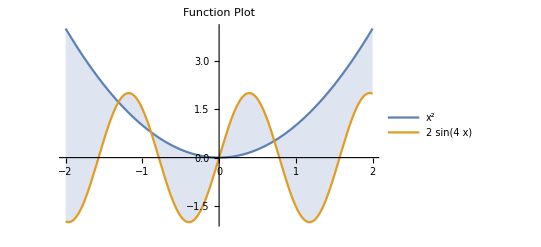

```mathematica
plot = Plot[ { x^2, 2Sin[4 x] }, {x,-2,2}, 
PlotLabel -> Style["Function Plot", "Subtitle", Gray], 
PlotLegends->"Expressions", 
Filling-> {1-> {2}}
]
```

... find the x values for graph intersections.

```mathematica
NSolveValues[ x^2 == 2 Sin[4 x], x, Reals]
```

{-1.31179,-0.886309,0.,0.719873}

And “map” a function over this list to generate a list of tuples (aka points).

```mathematica
points = % //Map[ Function[x, {x, x^2}]]
```

{{-1.31179,1.72078},{-0.886309,0.785544},{0.,0.},{0.719873,0.518218}}

These points can then be added as an “epilog” to the plot.

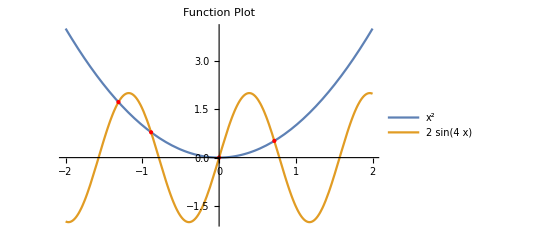

```mathematica
Plot[ { x^2, 2Sin[4 x] }, {x,-2,2}, 
PlotLabel -> Style["Function Plot", "Subtitle", Gray], 
PlotLegends->"Expressions", 
(*Filling-> {1-> {2}},*) 
Epilog->{
Red,
PointSize[Medium],
Point @ points
}
]
```

#### Differential Equations

We can solve elementary symbolic differential equations, for example the following third order expontential delay system:

```mathematica
DSolve[
{
x1'[t] == inflow - x1[t]/(delayTime/3),
x2'[t] == x1[t]/(delayTime/3)-x2[t]/(delayTime/3),
x3'[t] == x2[t]/(delayTime/3)-x3[t]/(delayTime/3),
x1[0]==initialX1,
x2[0]== initialX2,
x3[0]== initialX3
}
,
{ x1, x2, x3}
,
t
]//First /* TableForm
```

x1→Function[{t},1/3 ⅇ^(-(3 t)/delayTime) (-delayTime inflow+delayTime ⅇ^((3 t)/delayTime) inflow+3 initialX1)]
x2→Function[{t},(ⅇ^(-(3 t)/delayTime) (-delayTime^2 inflow+delayTime^2 ⅇ^((3 t)/delayTime) inflow+3 delayTime initialX2-3 delayTime inflow t+9 initialX1 t))/(3 delayTime)]
x3→Function[{t},(ⅇ^(-(3 t)/delayTime) (-2 delayTime^3 inflow+2 delayTime^3 ⅇ^((3 t)/delayTime) inflow+6 delayTime^2 initialX3-6 delayTime^2 inflow t+18 delayTime initialX2 t-9 delayTime inflow t^2+27 initialX1 t^2))/(6 delayTime^2)]

#### Knowledge Representation & Access

A tremendous amount of data can be immediately accessed and processed.

9.63142×10^6 km^2

Often we are interested in a subset of entities, i.e., we apply a filter or a query.

```mathematica
EntityClass["Country","EuropeanUnion"]//EntityList
```

{Austria,Belgium,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Ireland,Italy,Latvia,Lithuania,Luxembourg,Malta,Netherlands,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden}

What are the properties that we may be interested in for the entity “country”?

```mathematica
EntityProperties["Country"]//Short
```

{adjusted net national income,seasonal bank borrowings from Fed, plus adjustments,regions,adult population,obese adults,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,aggregate home value, householder 25 to 34 years,aggregate home value, householder 35 to 64 years,aggregate home value, householder 65 years and over,aggregate household income,aggregate weekly hours index,agricultural irrigated land fraction,agricultural land fraction,agricultural production index,agricultural production per capita index,agricultural products,consumption,consumption per capita,harvest area,harvest area per capita,production,production per capita,average yield,yield per capita,arrivals by air,aircraft carriers,air force,airports,air transport,alcohol fuel,total primary energy,alternate names,AM radio stations,annual annulments,annual births,annual deaths,annual divorces,annual HIV/AIDS deaths,annual marriages,antenatal care coverage,annual-crop land area,annual-crop land fraction,total area,armored infantry fighting vehicles,armored personnel carriers,army,artillery,attack helicopters,automobile production,average hourly earnings,average length of stay,average number of meetings with tax officials,average time to clear exports through customs,average weekly hours,average weekly overtime hours,aviation gasoline,bankers acceptance rate,bank prime loan rate,bank prime loan rate changes,benefits cost index,birth rate fraction,births attended by skilled health personnel,births by caesarean section,book titles published,bordering countries/regions,shared border lengths,full boundary length,«611»,time to prepare and pay taxes,time to resolve insolvency,time zones,current tobacco use among adolescents,current tobacco use among adults,total annual visitors,total borrowings,total registered businesses,total business inventory,total business tax rate,total fertility rate,trade value,trade balance,trade deficit,trade value added,trade-weighted exchange index,transportation value added,traveler's checks outstanding,treasury security,treasury average yield,treasury deposits,treasury securities composite rate,UN code,unemployed people,unemployment average duration,unemployment median duration,unemployment rate,unilateral current transfers,unit labor cost,unit nonlabor cost,UN number,unpaved airport lengths,unpaved airports,unpaved road length,unweighted sample housing units,unweighted sample population,uranium,change in US owned assets abroad,GDP value added,losses due to electrical outages,vault cash,vehicle sales,buses in use,buses in use per road length,buses in use per population,motorcycles in use,motorcycles in use per road length,motorcycles in use per population,passenger cars in use,passenger cars in use per road length,passenger cars in use per population,total vehicles in use,total vehicles in use per road length,total vehicles in use per population,trucks and vans in use,trucks and vans in use per road length,trucks and vans in use per population,total rate of violent crime,total number of violent crimes,vulnerable employment,vulnerable employment fraction,wage and salaried workers,wage and salaried workers fraction,wage cost index,water area,arrivals by sea,water productivity,waterway length,employment,wholesale price index}

So let’s get the population in 2000 for the countries in the EU and make this a nice looking table using the UN country code to identify countries.

```mathematica
EntityClass["Country","EuropeanUnion"]//RightComposition[
EntityList,
Map @ Function[ country, <|EntityProperty["Country", "UNCode"]@country ->EntityProperty["Country", "Population", { "Date"-> 2000 }]@country|> ],
Dataset
]
```

#### Further Information

An Elementary Introduction to the Wolfram Language

Wolfram Language: Fast Introduction for Programmers

Wolfram Language: Fast Introduction for Math Students

Wolfram Language & System Documentation Center

### Building modern data science techniques into modeling software versus importing models into mature data science environments

Houghton and Siegel (2015) in introducing PySD come to the conclusion: 
It makes much more sense to import models to powerful data science environments than to wait until methods are eventually integrated in the system dynamics software.

So how is system dynamics and systems modeling in general integrated into the Wolfram Language?

Systems Modeling is found in the section “Engineering Data & Computation”:

The guide on “System Model Analytics & Design” gets us right into this workshops further topics.

## Model Creation and Import

How can we create system models in the WL and how can we access models that are already built?

### Object–oriented modeling using pre-built components in Wolfram SystemModeler (a quick recap of Workshop #231)

#### Hello World! example using component-based modeling

In Workshop #231 we introduced component-based modeling in Wolfram System Modeler—starting out with a simple Hello World! example.

-Graphics-

#### Using classes from the Business Simulation Library (BSL)

The classes for building system dynamics models came from the Business Simulation Library (BSL), which is a modern implementation of system dynamics in Modelica making use of acausal “physical” connectors (think: pipe fittings).

-Graphics-

#### Building larger models in a hierarchical fashion

We then showed how larger models can be build in a distributed, object-oriented fashion that is especially amenable to working in a team, to using version control systems like Git, and to documenting models in an integrated fashion (documentation needs to be integrated into the modeling environment, not a separate tool).

-Graphics-

### Creating models programmatically in the Wolfram Language

We will not address creating models programmatically in the WL in this workshop, but provide just a few pointers.

#### Connect pre-built components from within a program

You can use ConnectSystemModelComponents to use pre-built components from a library and connect them to build a SystemModel.

#### Build a model from a systems model

Using CreateSystemModel you can turn a systems model, i.e., a model following a different modeling paradigm, into a SystemModel that can be used and connected as a Modelica model. Systems models can be one of the following:

StateSpaceModel

TransferFunctionModel

AffineStateSpaceModel

NonlinearStateSpaceModel

DiscreteInputOutputModel

Using this you can integrate(partial) models from other domains into your Modelica models—after all, whatever your background, we are interested in dynamical systems.

#### Create a data model by sampling from a function

By sampling from a function to come up with an interpolated curve, CreateDataSystemModel let’s you build an information source for other models to use.

### Importing models (→Connectivity)

#### Import a textual model written in Modelica

In Workshop #231 we started out with a textual Modelica model for a teacup cooling to room temperature.
Let’s import it as a string (note that strings inside are” escaped” using \ .

```mathematica
$teaCupTextualModel = ImportString[
"model TeaCupTextual \"Textual model for cooling cup\"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = \"degC\") = 90 \"Initial temperature in the cup\";
  parameter Real tempRoom(unit = \"degC\") = 20 \"Temperature in the room\";
  parameter Time adjTime(displayUnit = \"min\") = 600 \"Time constant for adjustment process\";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = \"degC\") \"Temperature in the cup is modeled as a stock\";
  Rate heatFlow(displayUnit = \"1/min\") \"Outflow of heat from the cup\";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
end TeaCupTextual;"
,
"MO" (* type MO for Modelica models *)
]
```

-Graphics-

Looking at the Modelica code after the input shows that it is interpreted correctly as a model written in the Modelica language.

```mathematica
$teaCupTextualModel["ModelicaDisplay"]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
end TeaCupTextual;

#### Importing SystemModeler Archives (.sma) or directly accessing SystemModeler models

In case we do not have SystemModeler installed, we need to import a library or larger model (package.mo) and its data. This is best done using Import or CloudImport and the .sma format that packs models as an archive.

$class = Import[ "filename", "SMA"];
$class = CloudImport[ "uri" ];

If the model has dependencies and is not distributed as a “total model” then we have to make sure that all the dependent libraries are imported as well.

If we have loaded a library or a modeling project in a local installation of SystemModel we can immediately access it.

```mathematica
$teaCupComponentBasedModel = SystemModel["ISDC2022_Workshops.Examples.TeaCupComponentBased1"]
```

-Graphics-

## Model Exploration & Simulation

### A SystemModel has (lots of) properties that we can inspect before we simulate it

Once we have loaded (or created) a SystemModel, we can explore its properties.

```mathematica
$teaCupComponentBasedModel["Properties"]//OperatorApplied[Partition][3]//OperatorApplied[Grid][Alignment-> Left]
```

AlgebraicVariables | Balanced | Children
Components | Connections | Connectors
Description | Diagram | DiscreteVariables
Documentation | DocumentationURL | Domain
DomainChart | ExtendsModels | GroupedInitialValues
InheritedComponents | InheritedConnections | InheritedConnectors
InheritedPlotNames | InheritedPlots | InitialEquations
InitialSeedings | InitialValues | InputVariables
LocalComponents | LocalConnections | LocalConnectors
LocalPlotNames | LocalPlots | ModelicaDisplay
ModelicaIcon | ModelicaString | ModelName
ModelsContaining | ModelsExtending | OutputVariables
ParameterNames | ParameterValues | Parent
PlotNames | Plots | PropertyAssociation
PropertyDataset | Siblings | SimulationModel
SimulationSettings | SourceFile | Specialization
StateVariables | Summary | SystemEquations
SystemVariables | Thumbnail | TopParameterNames

#### Summary

A nice summary is given.

```mathematica
$teaCupComponentBasedModel["Summary"]
```

#### Icon View

... look at its icon.

```mathematica
$teaCupComponentBasedModel["ModelicaIcon"]//OperatorApplied[ImageResize][Small]
```

-Graphics-

#### Diagram View

... inspect a model’s diagram.

```mathematica
$teaCupComponentBasedModel["Diagram"]
```

-Graphics-

#### Text View

Modelica code can be accessed as a pure string.

```mathematica
$teaCupTextualModel["ModelicaString"]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
end TeaCupTextual;

... or in a color-coded version.

```mathematica
$teaCupTextualModel["ModelicaDisplay"]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
end TeaCupTextual;

#### A closer look at model structure and equations

Which components are used in our model?

```mathematica
bslSystemModelComponentDatabase[ $teaCupComponentBasedModel]//Dataset
```

How are they connected to each other?

```mathematica
$teaCupComponentBasedModel["Connections"]
```

{adjTime.y<->heatLoss.u2,heatLoss.y<->losingHeat.u,losingHeat.portB<->cloud.massPort,tempCup.outflow<->losingHeat.portA,tempCup.y2<->tempDifference.u1,tempDifference.y<->heatLoss.u1,tempRoom.y<->tempDifference.u2}

How does this look in a Graph ?

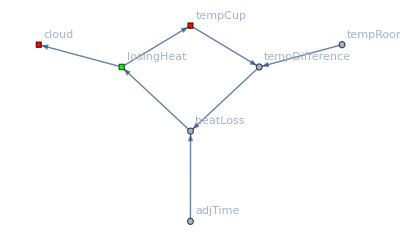

```mathematica
bslSystemModelGraph[ $teaCupComponentBasedModel ]
```

Finally, we can inspect the equations in the model ...

```mathematica
$teaCupComponentBasedModel["SystemEquations",Method-> {"Elimination"-> All}]//DeleteCases[WhenEvent[ ___]]//TableForm
```

-losingHeat.B_rate IndependentPhysicalQuantity[Rate][t]==(tempDifference.y IndependentPhysicalQuantity[][t])/(adjTime.value Time)
tempDifference.y IndependentPhysicalQuantity[][t]==-tempRoom.value IndependentPhysicalQuantity[]+tempCup.x IndependentPhysicalQuantity[][t]
losingHeat.y IndependentPhysicalQuantity[Rate][t]==If[losingHeat.useA_rate IndependentPhysicalQuantity[][t]&&losingHeat.useB_rate IndependentPhysicalQuantity[][t],-losingHeat.B_rate IndependentPhysicalQuantity[Rate][t],0]
tempCup.x IndependentPhysicalQuantity[]'[t]==-losingHeat.y IndependentPhysicalQuantity[Rate][t]

... and find out about the (top level) parameters for a model and their values.

```mathematica
$teaCupTextualModel["TopParameterNames"]
```

{initTempCup IndependentPhysicalQuantity[],tempRoom IndependentPhysicalQuantity[],adjTime Time}

```mathematica
$teaCupComponentBasedModel["ParameterValues"]//TableForm
```

modelSettings.modelTimeHorizon Time→3600
tempCup.maxValue IndependentPhysicalQuantity[]→1.79769×10^308
tempCup.minValue IndependentPhysicalQuantity[]→-1.79769×10^308
tempCup.initialValue IndependentPhysicalQuantity[]→90
losingHeat.rate IndependentPhysicalQuantity[Rate]→0
tempRoom.value IndependentPhysicalQuantity[]→20
adjTime.value Time→1200

## Helper Functions

#### bslSystemModelComponentDatabase

```mathematica
ClearAll[bslSystemModelComponentDatabase];
bslSystemModelComponentDatabase[ model_SystemModel ]:=model["Components"]//RightComposition[
OperatorApplied[Cases][ Element[ name_String, SystemModel[ component_String, True]]:> Association["Name"-> name, "Class" -> component]]
];
```

#### bslSystemModelGraph

```mathematica
ClearAll[ bslSystemModelGraph ];
bslSystemModelGraph::usage = "bslSystemModelGraph[model] will return a graph with causal connections shown as directed edges.";
bslSystemModelGraph[ model_SystemModel ] := bslSystemModelGraph[ model["Connections"], bslSystemModelComponentDatabase[ model ] ];
bslSystemModelGraph[ connections_ , componentDatabase_ ]:=
With[
{
inputPattern =  ___~~".u"~~___~~EndOfString,
outputPattern = ___ ~~ ".y" ~~ ___ ~~ EndOfString,
stockQ = Function[ key, componentDatabase//RightComposition[
Query[ SelectFirst[ #Name ==key&], "Class" ],
OperatorApplied[Not@*StringFreeQ]["Stocks"| "Cloud"]
] 
],
flowQ = Function[ key, componentDatabase//RightComposition[
Query[ SelectFirst[ #Name ==key&], "Class" ],
OperatorApplied[Not@*StringFreeQ]["Flows"|"SourcesOrSinks" ]
] 
],
toVertices=Function[ edges, edges//RightComposition[
ReplaceAll[ DirectedEdge[ a_, b_]| UndirectedEdge[a_, b_ ] :>Sequence[a,b]],
Union
]
]
}
,
(* replace input <-> output and output <-> input with directed edges *)
connections//RightComposition[
ReplaceAll[ c1_String <-> c2_String :> c2->c1 /; And[
StringMatchQ[c1, inputPattern ],
StringMatchQ[c2, outputPattern ]
]
],
ReplaceAll[ c1_String <-> c2_String :> c1 -> c2 /; And[
StringMatchQ[c1, outputPattern ],
StringMatchQ[c2, inputPattern ]
]
],
(* get rid of connector names at the end of component names *)
ReplaceAll[x_String :>StringDelete[x,"." ~~___]],
(* make flow <-> stock connections directed edges *)
ReplaceAll[ f_String <-> s_String | s_String <->f_String :> f-> s /; And[
stockQ @ s,
flowQ @ f
]
],
(* draw a graph *)
Function[ edges,
With[
{ 
stockList = Select[ toVertices @ edges,stockQ ],
flowList = Select[ toVertices @ edges, flowQ ]
}
, 
Graph[ edges, 
VertexLabels-> "Name",
VertexShapeFunction-> Union[ Thread[ stockList -> "Square" ], Thread[ flowList -> "Square" ]],
VertexStyle-> Union[ Thread[ stockList -> Red ], Thread[ flowList -> Green ] ]
]
]
]
]
]
```